$Aborted

$Aborted

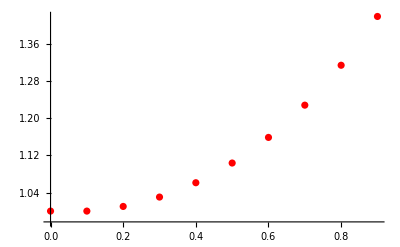

```mathematica
f[x_,y_]:=x*y;

f_x[y_]:=y;

f_y[t_,x_,y_]:=-y/t-x;

(*Метод Эйлера для уравнения*)
a=0.0;
b=1;
h=0.1;
n=(b-a)/h;
x=Table[0.0,{i,1,IntegerPart[n]}];
y=Table[1.0,{i,1,IntegerPart[n]}];
For[i=1,i<IntegerPart[n],i++,x[[i+1]]=x[[i]]+h;
y[[i+1]]=y[[i]]+h*f[x[[i]],y[[i]]]];
x2=Range[0,1,0.01];
y2=Exp[x2^2/2];
ListLinePlot[Transpose[{x2,y2}],PlotStyle->Blue,PlotRange->All];
ListPlot[Transpose[{x,y}],PlotStyle->Red,PlotRange->All]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ClearAll["Global`*"]
```